{{φ→InterpolatingFunction[{{…, -20., 20., …}, {0., 15.}}, <>]}}

Field Amplitude:

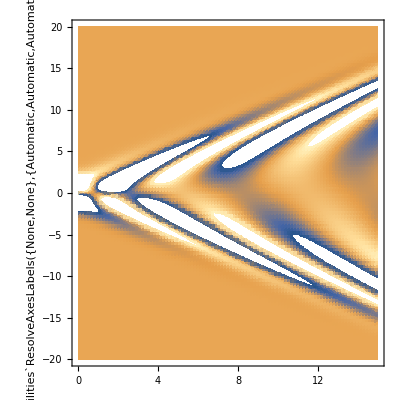

Hamiltonian Density:

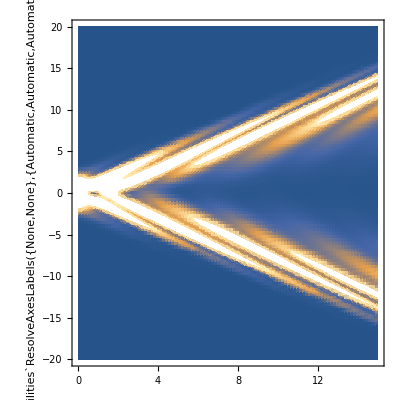

```mathematica
m=1;
g=1/2;
λ=1/2;
time=15;
X=20;
V=m/2*φ[x,t]^2+g*φ[x,t]^3+λ*φ[x,t]^4;
ℒ=1/2*(D[φ[x,t],t]^2-D[φ[x,t],x]^2)-V;
ℋ=1/2*(D[φ[x,t],t]^2+D[φ[x,t],x]^2)+V;
Needs["VariationalMethods`"]
eqs=EulerEquations[ℒ,φ[x,t],{x,t}];
s=NDSolve[{eqs,φ[x,0]==x Exp[-x^2/2],Derivative[0,1][φ][x,0]==0,φ[-X,t]==φ[X,t]},φ,{x,-X,X},{t,0,time}]
"Field Amplitude:"
DensityPlot[Evaluate[φ[x,t]/.s],{t,0,time},{x,-X,X},WorkingPrecision->20,PlotPoints->100]
Animate[Show[Plot[φ[x,t]/.s,{x,-X,X},PlotRange->{-1,1},Filling->Axis],BoxRatios->Automatic],{t,0,time},AnimationRate->1, AnimationRunning->False,RefreshRate->30]
"Hamiltonian Density:"
DensityPlot[Evaluate[ℋ/.s],{t,0,time},{x,-X,X},WorkingPrecision->20,PlotPoints->100]
```